```mathematica
Vollständiges Modell
```

```mathematica
<<Statistics`ContinuousDistributions`
```

Get::noopen: Cannot open Statistics`ContinuousDistributions`.

$Failed

```mathematica
Clear["Global`*"];
ar=26; (* Number of reactions *)
am=23; (* Number of metabolites *)
$TextStyle=FontSize->14;  

(* List of parameters and rates *)

(*parameters*)
ConcAdpPF=0.001;ConcAtpPF=0.002;ConcB13pgPF=0.0001;ConcDhapPF=0.0001;ConcF16bpPF=0.0001;ConcF6pPF=0.0001;ConcG6pPF=0.0001;ConcGapPF=0.0001;ConcGlcEX=0.005;ConcGlcPF=0.0001;ConcGly3pPF=0.0001;ConcGlyEX=0.00015;ConcLacEX=0.002;ConcLacPF=0.0001;ConcNadPF=0.0025;ConcNadhPF=0.0005;ConcP2gPF=0.0001;ConcP3gPF=0.0001;ConcPepPF=0.0001;ConcPyrEX=0.0002;ConcPyrPF=0.0001;
KPFvGLCtr=0.000213;KadpPFvHK=0.000846735;KadpPFvPFK=0.00074176;KadpPFvPGK=0.00015;KadpPFvPK=0.000317;KatpPFvHK=0.00069647;KatpPFvPFK=0.0007862;KatpPFvPGK=0.00077;Kb13pgPFvGAPDH=2.359*^-05;Kb13pgPFvPGK=1.34*^-05;KdPFvLACtr=0.005;KdPFvPYRtr=0.0007;KdhapPFvALD=0.00011;KdhapPFvG3PDH=0.00034;KdhapPFvTPI=0.001954;KeqPFvALD=9*^-05;KeqPFvENO=4.6;KeqPFvG3PDH=32600.0;KeqPFvHK=1310.0;KeqPFvPGI=0.33;KeqPFvPGK=3200.0;KeqPFvPGM=0.19;KeqPFvTPI=0.04545;Kf16bpPFvALD=6.84*^-05;Kf16bpPFvPFK=0.003626;Kf6pPFvPFK=0.00109454;Kf6pPFvPGI=9.6651*^-05;Kg3pPFvG3PDH=0.00398;Kg6pPFvHK=4.3*^-05;Kg6pPFvPGI=0.00100774;KgapPFvALD=4.6*^-05;KgapPFvGAPDH=0.000917;KgapPFvTPI=0.000337;KglcPFvHK=0.000168613;Ki1CytGlcTr=8.86746353676*^-08;Ki2CytGlcTr=2.07687280949*^-05;KiadpPFvPK=0.002;KiatpPFvHK=0.026;KiatpPFvPK=0.00182;KilacPFvPYRtr=0.000358;KipepPFvPK=0.00292;KipepPFvTPI=1.59*^-05;KipyrPFvLACtr=0.00163;KipyrPFvPK=0.105;KlacPFvLACtr=0.0038;KlacPFvLDH=0.003611;KmPFvATPASE=0.0045;KnadPFvG3PDH=0.00051;KnadPFvGAPDH=0.0005662;KnadPFvLDH=0.000234;KnadhPFvG3PDH=9*^-05;KnadhPFvGAPDH=2.87*^-05;KnadhPFvLDH=4.6*^-05;Kp2gPFvENO=0.000521;Kp2gPFvPGM=0.000318;Kp3gPFvPGK=0.000267;Kp3gPFvPGM=0.00173;KpepPFvENO=0.00129;KpepPFvPK=0.000406;KpyrPFvLDH=0.000133;KpyrPFvPYRtr=0.0157;LPFvPK=0.255;VPFvALD=0.0569593147718;
VPFvATPASE=(*0.345*)(*0.005027754423905*)0.15;
VPFvENO=0.286295503195;VPFvGAPDH=0.656263383259;VPFvGLCtr=0.0469;VPFvHK=0.083;VPFvLACtr=0.598;VPFvPFK=0.41;VPFvPGI=0.800428265477;VPFvPGM=0.186937901488;VPFvPK=0.762;VPFvPYRtr=0.216;VPFvTPI=1.50599571726;VfPFvG3PDH=0.012;VfPFvLDH=0.542612419668;VrPFvGAPDH=0.243199143455;VrPFvLDH=0.290792291203;VrPFvPGK=0.353533190557;alphaPFvGLCtr=0.91;
cytb=0.0000;
h=4.0;kPFvGLYtr=2.0;pHConversionFactor=1.0;
phEX=7.1;
glcEX=1000*0.45/90;glyEX=1000*0.013499999999999998/90;lacEX=1000*0.18/90;pyrEX=1000*0.018000000000000002/90;Vex=1000;Vpf=1000; 

Nasal=125;Ksal=5;Clsal=130;pHsal=7.1;Ap= 65;F=96485.33289;Cm=0.01;zH=1;zNa=1;zK= 1;zCl= -1;phiKNaCl=0.92;Ysal= 70.8;R= 8.3144598;T= 310;Kcp= 1.5*10^(-12);zY= 0;bcp= 54.186505397223954;bcbp= 368.00427412088493;bcpkap= 7.172371123455439;KmNaHpumpHsal= 4.0976860324961274*10^(-06); KIPfATP4Hp= 7.104526671732046*10^(-06);KmNaHpumpNap= 0.6840120477024911; vmaxNaHpump= 7.703685608134962*10^(-08); sPfATP4H= 1; sPfATP4Na= 1; kVTypepumpEp0= -0.0999999978223507; vmaxVTypepump= (6.7024838393612216*10^(-06))/4; kexpVTypepump= 4.506272510067805; KmVTypepumpHp= 0.0022634396699840083; 
sVtypeH= 4; 
sVtypeHexponent= 1; KIVTypeHsal= 0.0023696056686678623; kexpPfKchannel= 28.622973488515083; kPfKchannelEp0= -0.04375853867278892; keqPfKchannel= 0.9161672755776934; kPfKchannel= 6.828228224275584*10^(-12); kPfHClcot= 8.272568285457453*10^(-11); hPfHClKIHp= 4.79709902173202; KmPfHClClrbc= 7.8; sPfHClCl= 1; sPfHClH= 1; KIPfHClHp= 2.928504560811203*10^(-05); PHp= 2.6440241005783135*10^(-05); PNap= 1.0346068948554299*10^(-10); PKp= 0; PClp= 6.696605288022938*10^(-11); solidVp= 22.05; cipargamin= 0; concanamycin= 0;bafilomycin= 0; KIcip= 0.5*10^(-6); KIcona= 1.5*10^(-6); KIbaf= 2*10^(-6); caesium= 0; KIcs= 0.05; hclinhi= 0; KIhclinhi= 0.05; mercury= 0; KImercury= 0.35; 
Atpss= 2.5; KmAtpAtp4= 0.23; KmAtpVType= 0.2; sPfATP4ATP= 1.0; sVtypeATP= 1;
at=3.0;nt=3.0;

(*rates*)
v[1]=1/60((VPFvALD*m[3]*(1-(m[2]*m[7])/(KeqPFvALD*Vpf*m[3])))/(Kf16bpPFvALD*(1+m[2]/(KdhapPFvALD*Vpf)+m[3]/(Kf16bpPFvALD*Vpf)+m[7]/(KgapPFvALD*Vpf)+(m[2]*m[7])/(KdhapPFvALD*KgapPFvALD*Vpf^2))));v[2]=1/60((VPFvATPASE*m[21]^5)/(KmPFvATPASE^5*Vpf^4*(1+m[21]^5/(KmPFvATPASE^5*Vpf^5))));
v[3]=1/60((VPFvENO*m[10]*(1-m[12]/(KeqPFvENO*m[10])))/(Kp2gPFvENO*(1+m[10]/(Kp2gPFvENO*Vpf)+m[12]/(KpepPFvENO*Vpf))));
v[4]=1/60((VfPFvG3PDH*m[2]*m[22]*(1-(m[5]*m[23])/(KeqPFvG3PDH*m[2]*m[22])))/(KdhapPFvG3PDH*KnadhPFvG3PDH*Vpf*(1+m[2]/(KdhapPFvG3PDH*Vpf)+m[5]/(Kg3pPFvG3PDH*Vpf))*(1+m[22]/(KnadhPFvG3PDH*Vpf)+m[23]/(KnadPFvG3PDH*Vpf))));
v[5]=1/60((-((VrPFvGAPDH*m[1]*m[22])/(Kb13pgPFvGAPDH*KnadhPFvGAPDH*Vpf))+(VPFvGAPDH*m[7]*m[23])/(KgapPFvGAPDH*KnadPFvGAPDH*Vpf))/((1+m[1]/(Kb13pgPFvGAPDH*Vpf)+m[7]/(KgapPFvGAPDH*Vpf))*(1+m[22]/(KnadhPFvGAPDH*Vpf)+m[23]/(KnadPFvGAPDH*Vpf))));v[6]=1/60(((glcEX*Vpf*VPFvGLCtr)/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)-(VPFvGLCtr*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr))/(1+(glcEX*(1+cytb/Ki2CytGlcTr))/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)+((1+cytb/Ki2CytGlcTr)*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vpf)+(alphaPFvGLCtr*glcEX*m[8])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr^2*Vex*Vpf)));
v[7]=1/60(kPFvGLYtr*Vpf*(-(glyEX/Vex)+m[5]/Vpf));v[8]=1/60((VPFvHK*m[21]*(1-(m[20]*m[6])/(KeqPFvHK*m[21]*m[8]))*m[8])/(KatpPFvHK*KglcPFvHK*Vpf*(1+m[20]/(KadpPFvHK*Vpf)+m[21]/(KatpPFvHK*Vpf))*(1+m[21]/(KiatpPFvHK*Vpf))*(1+m[6]/(Kg6pPFvHK*Vpf)+m[8]/(KglcPFvHK*Vpf))));v[9]=1/60(KdPFvLACtr*(1-((pHConversionFactor/10^phEX)*lacEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[9]))*m[9]+(VPFvLACtr*(1-((pHConversionFactor/10^phEX)*lacEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[9]))*m[9])/(KlacPFvLACtr*(1+lacEX/(KlacPFvLACtr*Vex)+pyrEX/(KipyrPFvLACtr*Vex)+m[9]/(KlacPFvLACtr*Vpf)+m[13]/(KipyrPFvLACtr*Vpf))));v[10]=1/60((-((VrPFvLDH*m[9]*m[23])/(KlacPFvLDH*KnadPFvLDH*Vpf))+(VfPFvLDH*m[22]*m[13])/(KnadhPFvLDH*KpyrPFvLDH*Vpf))/((1+m[22]/(KnadhPFvLDH*Vpf)+m[23]/(KnadPFvLDH*Vpf))*(1+m[9]/(KlacPFvLDH*Vpf)+m[13]/(KpyrPFvLDH*Vpf))));v[11]=1/60((VPFvPFK*m[21]*m[4])/(KatpPFvPFK*Kf6pPFvPFK*Vpf*(1+m[21]/(KatpPFvPFK*Vpf))*(1+m[20]/(KadpPFvPFK*Vpf)+m[21]/(KatpPFvPFK*Vpf))*(1+m[3]/(Kf16bpPFvPFK*Vpf)+m[4]/(Kf6pPFvPFK*Vpf))));v[12]=1/60((VPFvPGI*(1-m[4]/(KeqPFvPGI*m[6]))*m[6])/(Kg6pPFvPGI*(1+m[4]/(Kf6pPFvPGI*Vpf)+m[6]/(Kg6pPFvPGI*Vpf))));v[13]=1/60((KadpPFvPGK*Kb13pgPFvPGK*KeqPFvPGK*VrPFvPGK*m[21]*(-1+(KeqPFvPGK*m[20]*m[1])/(m[21]*m[11]))*m[11])/(KatpPFvPGK^2*Kp3gPFvPGK^2*Vpf*(1+m[20]/(KadpPFvPGK*Vpf)+m[21]/(KatpPFvPGK*Vpf))*(1+m[1]/(Kb13pgPFvPGK*Vpf)+m[11]/(Kp3gPFvPGK*Vpf))));v[14]=1/60((VPFvPGM*(1-m[10]/(KeqPFvPGM*m[11]))*m[11])/(Kp3gPFvPGM*(1+m[10]/(Kp2gPFvPGM*Vpf)+m[11]/(Kp3gPFvPGM*Vpf))));v[15]=1/60((VPFvPK*m[20]*m[12])/(KadpPFvPK*KpepPFvPK*Vpf*(1+m[20]/(KadpPFvPK*Vpf))*(1+m[12]/(KpepPFvPK*Vpf))*(1+LPFvPK*(1+(m[20]/(KiadpPFvPK*Vpf)+m[21]/(KiatpPFvPK*Vpf))^h)*(1+(m[12]/(KipepPFvPK*Vpf)+m[13]/(KipyrPFvPK*Vpf))^h))));v[16]=1/60(KdPFvPYRtr*(1-((pHConversionFactor/10^phEX)*pyrEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[13]))*m[13]+(VPFvPYRtr*(1-((pHConversionFactor/10^phEX)*pyrEX*Vpf)/((pHConversionFactor/10^m[14])*Vex*m[13]))*m[13])/(KpyrPFvPYRtr*(1+lacEX/(KilacPFvPYRtr*Vex)+pyrEX/(KpyrPFvPYRtr*Vex)+m[9]/(KilacPFvPYRtr*Vpf)+m[13]/(KpyrPFvPYRtr*Vpf))));v[17]=1/60((VPFvTPI*m[2]*(1-m[7]/(KeqPFvTPI*m[2])))/(KdhapPFvTPI*(1+m[2]/(KdhapPFvTPI*Vpf)+m[7]/(KgapPFvTPI*Vpf)+m[12]/(KipepPFvTPI*Vpf))));
v[18]= 
vmaxNaHpump*((Atpss/(KmAtpAtp4+Atpss))^(-1))*((m[17]/(KmNaHpumpNap*(2^(1/sPfATP4Na)-1)*(1+( 1*10^3*10^(-m[14]))/KIPfATP4Hp)+m[17]))^sPfATP4Na)*(((1*10^3*10^(-pHsal))/(KmNaHpumpHsal*(2^(1/sPfATP4H)-1)+(1*10^3*10^(-pHsal))))^sPfATP4H)*(m[21]/(KmAtpAtp4+m[21]))^1*(1/(1+cipargamin/KIcip));
v[19]=
vmaxVTypepump*((Atpss/(KmAtpVType+Atpss))^(-1))*((m[21]/(KmAtpVType+m[21])))^1*((( 1*10^3*10^(-m[14]))/(( 1*10^3*10^(-m[14]))+KmVTypepumpHp))^sVtypeHexponent)*(1/(1+Exp[-kexpVTypepump*(m[15]-kVTypepumpEp0)]))*(1/(1+(1*10^3*10^(-pHsal))/KIVTypeHsal))*(1/(1+concanamycin/KIcona))*(1/(1+bafilomycin/KIbaf));
v[20]=
kPfHClcot*((R*T*
Log[m[19]^sPfHClCl*( 1*10^3*10^(-m[14]))^sPfHClH/(Clsal^sPfHClCl*(1*10^3*10^(-pHsal))^sPfHClH)]+(sPfHClH-sPfHClCl)*F*m[15]))*((1/(1+(( 1*10^3*10^(-m[14]))/KIPfHClHp)^hPfHClKIHp)))*(1/(1+hclinhi/KIhclinhi));
v[21]=
 kPfKchannel*((1/(1+Exp[-kexpPfKchannel*(m[15]-kPfKchannelEp0)])))*((keqPfKchannel*m[15]-(R*T/(zK*F)*Log[(Ksal/m[18])]))*F)*(1/(1+caesium/KIcs));
v[22]=
(PHp*zH*m[15]*F/(R*T))*(( 1*10^3*10^(-m[14]))-(1*10^3*10^(-pHsal))*Exp[-zH*m[15]*F/(R*T)])/(1-Exp[-zH*m[15]*F/(R*T)]);
v[23]=
(PNap*zNa*m[15]*F/(R*T))*(m[17]-Nasal*Exp[-zNa*m[15]*F/(R*T)])/(1-Exp[-zNa*m[15]*F/(R*T)]);
v[24]= 
(PKp*zK*m[15]*F/(R*T))*(m[18]-Ksal*Exp[-zK*m[15]*F/(R*T)])/(1-Exp[-zK*m[15]*F/(R*T)]);

v[25]=
 (PClp*zCl*m[15]*F/(R*T))*(m[19]-Clsal*Exp[-zCl*m[15]*F/(R*T)])/(1-Exp[-zCl*m[15]*F/(R*T)]);
v[26]=1000000*Ap*Kcp*R*T*((( 1*10^3*10^(-m[14]))+(m[17]+m[18]+m[19])*phiKNaCl+m[16])-((1*10^3*10^(-pHsal))+(Nasal+Ksal+Clsal)*phiKNaCl+Ysal));


(* Calculation of elasticity coefficients *)
For[i=1,i≤ar,i++,
For[j=1,j≤am,j++,
drm[i,j]=D[v[i],m[j]]];
dvdsr[i]=Table[drm[i,j],{j,1,am}]];

dvds=Table[dvdsr[i],{i,1,ar}] ;


(* Reduced stoichiometric matrix, i.e. with conservation relations*)

(*v[1]=vPFvALD,v[2]=vPFvATPASE,v[3]=vPFvENO,v[4]=vPFvG3PDH,v[5]=vPFvGAPDH,v[6]=vPFvGLCtr,v[7]=vPFvGLYtr,v[8]=vPFvHK,v[9]=vPFvLACtr,v[10]=vPFvLDH,v[11]=vPFvPFK,v[12]=vPFvPGI,v[13]=vPFvPGK,v[14]=vPFvPGM,v[15]=vPFvPK,v[16]=vPFvPYRtr,v[17]=vPFvTPI, v[18]=JPfATP4salp,v[19]=JVtypesalp,v[20]=JPfHClsalp,v[21]=JPfKchannelsalp,v[22]=ghkfluxHsalp,v[23]=ghkfluxNasalp,v[24]=ghkfluxKsalp,v[25]=ghkfluxClsalp, v[26]=dVp*)
nr= {
{0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1} (*m[1]=b13pgPF'[t]*),
{1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1} (*m[2]=dhapPF'[t]*),
{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1} (*m[3]=f16bpPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1} (*m[4]=f6pPF'[t]*),
{0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1} (*m[5]=g3pPF'[t]*),
{0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1} (*m[6]=g6pPF'[t]*),
{1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1}(*m[7]=gapPF'[t]*),
{0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[8]=glcPF'[t]*),
{0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[9]=lacPF'[t]*),
{0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[10]=p2gPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[11]=p3gPF'[t]*),
{0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1}(*m[12]=pepPF'[t]*),
{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-1}(*m[13]=pyrPF'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-4,-1,0,-1,0,0,0,0}(*m[14]=pHp'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-1,-1,-1,0,-1,0}(*m[15]=Ep'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[16]=Yp'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,-1}(*m[17]=Nap'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,-1}(*m[18]=Kp'[t]*),
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,-1}(*m[19]=Clp'[t]*),
{0,1,0,0,0,0,0,1,0,0,1,0,-1,0,-1,0,0,1,1,0,0,0,0,0,0,-1} (*m[20]=adpPF'[t] (and atpPF=m[21]*),
{0,0,0,-1,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}(*m[22]=nadhPF'[t] (and nadPF=m[23])*)
};


(* Link matrix; 
can be identity matrix if the system has no conservation relations. See Introduction to Computational Models of Biochemical Reaction Networks Chapter 7, p.131. 
24 rows and 22 columns. Columns and rows are both metabolites. First 22 rows make up identity matrix. The last 2 rows include the conservation relations that are missing from the reduces stoichiometric matrix nr. atpPF is -1 from adpPF (21 row) and nadPF is -1 from nadh (22nd row).  
Link matrix connects the reduced stoich. with the full matrix. *)
lr={
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0}, 
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}
};

(*the calculations, first for the steady state *)
vv=Table[v[i],{i,1,ar}];
nv=nr.vv;
nvs=Table[nv[[i]]==0,{i,1,am-2}];

(*at==atp+adp, nt==nad+nadh*)
AppendTo[nvs,at==m[20]+m[21]]; (* conservation relations in this model *)
AppendTo[nvs,nt==m[22]+m[23]];(* conservation relations in this model *)
```

```mathematica
(*Print[nvs];*)
mlist=Table[{m[j],1},{j,1,am}];
Print["Concentrations"];
ss= {m[1]->0.0009147011821501772,m[2]->1.146826688548686,m[3]->1.0807675165140924,m[4]->0.2442875629619711,m[5]->0.5430856011907464,m[6]->0.7919537121170396,m[7]->0.04939027511395246,m[8]->0.7118042680062342,m[9]->3.543986034845742,m[10]->0.0502301506574996,m[11]->0.5096986411070364,m[12]->0.05682846185308859,m[13]->1.2637375949923095,m[14]->26.97908342521441,m[14]->7.300233858801494,m[15]->-0.09501494922750746,m[16]->116.6813160825033,m[17]->9.966007088312253,m[18]->130.06666744047135,m[19]->70.0963616218441, m[20]->0.44408791296742994,m[21]->2.5358878385733727,m[22]->0.05814876574923645,m[23]->2.9198029450297347}
Print["fluxes"];
fluss=Table[v[i]/.ss,{i,1,ar}]
```

Concentrations

{m[1]→0.000914701,m[2]→1.14683,m[3]→1.08077,m[4]→0.244288,m[5]→0.543086,m[6]→0.791954,m[7]→0.0493903,m[8]→0.711804,m[9]→3.54399,m[10]→0.0502302,m[11]→0.509699,m[12]→0.0568285,m[13]→1.26374,m[14]→26.9791,m[14]→7.30023,m[15]→-0.0950149,m[16]→116.681,m[17]→9.96601,m[18]→130.067,m[19]→70.0964,m[20]→0.444088,m[21]→2.53589,m[22]→0.0581488,m[23]→2.9198}

fluxes

{0.158634,0.134438,0.304165,0.0131029,0.304165,0.158634,0.0131029,0.158634,-1.18299×10^20,0.291062,0.158634,0.158634,0.304165,0.304165,0.304165,-2.09565×10^17,0.145531,6.86345×10^-8,3.80435×10^-28,-9.89166×10^-6,0.,-7.68942×10^-9,-4.72416×10^-8,0.,1.62768×10^-8,-0.0000125883}

```mathematica
(* now calculating elasticities and control coefficients *)
dvdss=dvds/.ss;
(*Jakobi Matrix*)
Print["Jacobi-Matrix"];
mr=nr.dvdss.lr ;
mra=Rationalize[mr,10^-20];
MatrixForm[mr]
```

Jacobi-Matrix

(-59043. | 0. | 0. | 0. | 0. | 0. | 6.57593 | 0. | 0. | 0. | 105.667 | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -119.337 | 21.1652
0. | 2.1347 | 0.292695 | 0. | 0.000747668 | 0. | -58.8066 | 0. | 0. | 0. | 0. | -1.72449 | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0.205747 | -0.00348871
0. | 0.268573 | -0.321454 | 0.554102 | 0. | 0. | 5.47563 | 0. | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -0.0443311 | -0.0270209
0. | 0. | 0.0287587 | -10.2348 | 0. | 3.03255 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0.0443311 | 0.0270209
0. | 0.00288769 | 0. | 0. | -0.034081 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -0.205747 | 0.00348871
0. | 0. | 0. | 9.68066 | 0. | -3.18864 | 0. | 0.183096 | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -0.036322 | 0.0129119
50.7372 | 2.13759 | 0.292695 | 0. | 0. | 0. | -65.3826 | 0. | 0. | 0. | 0. | -1.72449 | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -1.90763 | 0.0507216
0. | 0. | 0. | 0. | 0. | 0.156092 | 0. | -0.387968 | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0.036322 | -0.0129119
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -9.27275×10^18 | 0. | 0. | 0. | -2.16174×10^19 | 2.72394×10^20 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -10.6057 | 0.204454
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -14.7025 | 1.11879 | 1.95251 | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0. | 0.
58992.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.18387 | -106.785 | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 121.244 | -21.2159
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.51862 | 0. | -6.64766 | 2.41039×10^-7 | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -0.0666823 | 0.240213
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -3.52781×10^16 | 0. | 0. | 4.69514 | -8.0443×10^14 | 4.82541×10^17 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 10.6724 | -0.444666
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.90966×10^-7 | -7.2475×10^-8 | 0. | -4.42318×10^-10 | 0. | -3.04187×10^-9 | 0. | -2.25064×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.51061×10^-27 | -4.47421×10^-7 | 0. | -1.08072×10^-11 | -2.53551×10^-11 | -2.45179×10^-10 | 0. | -4.38674×10^-29
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.05702×10^-25 | -4.49298×10^-7 | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0. | -2.25064×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.07201×10^-25 | -1.13103×10^-7 | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.90966×10^-7 | 1.87454×10^-7 | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 0. | 0.
-58992.2 | 0. | -0.0287587 | 0.554102 | 0. | -0.156092 | 0. | 0.183096 | 0. | 0. | 105.667 | -4.69514 | 2.41039×10^-7 | 6.07824×10^-25 | 8.47544×10^-28 | -0.251305 | -0.2312 | -0.2312 | -0.2312 | -121.392 | 21.6928
-50.7372 | -0.00288769 | 0. | 0. | 0.000747668 | 0. | 6.57593 | 0. | 0.105949 | 0. | 0. | 0. | -0.317176 | 6.07201×10^-25 | 0. | -0.251305 | -0.2312 | -0.2312 | -0.2312 | 12.7191 | -0.258664)

```mathematica
imr=Inverse[mra];
nimr=N[imr];
MatrixForm[mr.nimr] (*checks if product of matrix and its inverse is approximately identity matrix*)
```

(1. | 6.77157×10^-14 | 1.71862×10^-15 | -6.93107×10^-15 | -1.39715×10^-16 | -1.89874×10^-15 | -3.46595×10^-14 | -9.87877×10^-15 | -4.17189×10^-35 | 2.05947×10^-14 | 5.55896×10^-14 | -3.1735×10^-15 | 6.22126×10^-33 | 2.05693×10^-7 | 2.72762×10^-6 | -5.20285×10^-6 | 1.30339×10^-6 | -6.57339×10^-6 | 2.04296×10^-6 | -2.90059×10^-14 | 1.21217×10^-15
-2.26148×10^-15 | 1. | -9.75747×10^-18 | -1.17595×10^-16 | -5.42012×10^-17 | -2.39476×10^-16 | 1.76833×10^-15 | 4.81881×10^-16 | -1.51062×10^-36 | 2.50501×10^-17 | -9.88186×10^-16 | -1.62051×10^-15 | 1.76754×10^-34 | -7.92226×10^-7 | 2.09131×10^-6 | 1.26248×10^-6 | 5.76864×10^-7 | -4.3093×10^-6 | 1.83336×10^-6 | 2.29475×10^-16 | -3.69485×10^-16
-1.23083×10^-15 | -6.42393×10^-16 | 1. | -1.93912×10^-16 | -3.46357×10^-18 | -8.5789×10^-17 | 2.04545×10^-15 | -2.9331×10^-17 | 6.6745×10^-37 | 2.76188×10^-16 | -1.04585×10^-15 | -1.68199×10^-15 | 1.18323×10^-34 | -6.77921×10^-7 | 2.77309×10^-6 | -3.9709×10^-6 | 7.98003×10^-7 | -5.93295×10^-6 | 4.37912×10^-7 | -1.20343×10^-16 | 1.31193×10^-17
-1.87779×10^-15 | 1.98304×10^-16 | -1.7113×10^-16 | 1. | -7.81213×10^-18 | -3.68897×10^-15 | -6.57668×10^-16 | -2.48225×10^-16 | 1.33089×10^-36 | -5.53744×10^-16 | -9.52547×10^-16 | -1.78746×10^-15 | -7.20177×10^-34 | -1.54643×10^-6 | 2.94884×10^-6 | -3.81601×10^-6 | 1.13536×10^-6 | -4.92304×10^-6 | 1.65262×10^-6 | 7.30966×10^-16 | 9.43207×10^-18
-2.60268×10^-15 | -1.96852×10^-16 | 3.36099×10^-17 | -1.0098×10^-16 | 1. | -2.10685×10^-16 | 1.47214×10^-15 | 1.16599×10^-16 | 4.29163×10^-37 | -2.60972×10^-16 | -9.70317×10^-16 | -9.729×10^-16 | -3.23089×10^-35 | -1.43201×10^-6 | 1.72327×10^-6 | -1.41987×10^-6 | 1.35656×10^-6 | -6.54667×10^-6 | 2.16457×10^-6 | 3.77678×10^-16 | 8.66239×10^-18
-1.75504×10^-15 | -5.16034×10^-16 | -1.98025×10^-17 | -2.31752×10^-15 | -1.04464×10^-17 | 1. | 1.27364×10^-15 | -4.55371×10^-16 | 4.53371×10^-37 | -4.05361×10^-16 | -2.52106×10^-16 | -1.30627×10^-15 | -1.0411×10^-34 | -1.90975×10^-6 | 2.15854×10^-6 | 2.37875×10^-6 | 1.58581×10^-6 | -6.53616×10^-6 | 7.17643×10^-7 | 6.35732×10^-16 | -6.06833×10^-17
-2.7765×10^-15 | 2.99139×10^-15 | -5.12898×10^-17 | -3.34503×10^-17 | -4.7739×10^-17 | -1.92481×10^-16 | 1. | 2.85025×10^-16 | -5.65646×10^-37 | -7.27793×10^-16 | -1.09639×10^-15 | -1.13122×10^-15 | -2.1922×10^-33 | -1.18182×10^-6 | 2.73893×10^-6 | -2.28214×10^-6 | 1.31182×10^-6 | -5.26656×10^-6 | 1.27255×10^-6 | 2.87717×10^-16 | -8.85502×10^-17
-1.32583×10^-15 | 1.64336×10^-17 | 4.40886×10^-17 | 1.04012×10^-16 | -1.69667×10^-18 | -2.05391×10^-16 | 1.41891×10^-16 | 1. | 2.85819×10^-38 | 1.41683×10^-16 | -8.44239×10^-16 | -1.28887×10^-15 | -1.06539×10^-34 | -3.14598×10^-7 | 1.65604×10^-6 | -2.53638×10^-6 | 3.47499×10^-7 | -4.31986×10^-6 | 1.37294×10^-6 | -2.51094×10^-17 | 2.94583×10^-17
92.1432 | 105.918 | -8.65769 | 108.925 | -0.0397068 | 150.516 | 305.716 | -51.7581 | 1. | -471.286 | -199.66 | 73.4467 | 3.52119×10^-14 | 1.52106×10^12 | -5.91605×10^11 | -5.60908×10^11 | 4.33598×10^11 | 2.07443×10^11 | -1.92113×10^12 | 181.022 | 11.1421
-2.43262×10^-15 | -2.45628×10^-16 | 3.97005×10^-17 | -1.09216×10^-16 | -6.68373×10^-18 | -2.25082×10^-16 | 7.31338×10^-16 | 7.74367×10^-17 | 6.3431×10^-37 | 1. | -9.79044×10^-16 | -1.29716×10^-15 | -3.07651×10^-34 | -1.58489×10^-7 | 2.86097×10^-6 | -3.89347×10^-6 | 1.92035×10^-6 | -5.428×10^-6 | 1.99894×10^-6 | 3.03509×10^-16 | 1.04273×10^-17
-7.40968×10^-15 | -2.4858×10^-14 | -1.98988×10^-15 | -1.58932×10^-15 | 1.39017×10^-15 | -9.88302×10^-16 | 9.7135×10^-15 | 1.48872×10^-14 | 1.29677×10^-35 | -6.28666×10^-14 | 1. | -1.21633×10^-14 | -4.08701×10^-33 | -1.39949×10^-7 | 1.32462×10^-6 | -3.54098×10^-6 | 1.21723×10^-6 | -2.50494×10^-6 | -1.12913×10^-7 | -9.2894×10^-15 | -9.18134×10^-15
-3.21242×10^-15 | -1.54561×10^-17 | 3.78444×10^-17 | -1.44355×10^-16 | 8.41019×10^-18 | 7.3653×10^-17 | -8.11529×10^-17 | 1.66136×10^-16 | 7.66924×10^-37 | -8.51728×10^-16 | -8.22402×10^-16 | 1. | -2.17745×10^-34 | -2.09202×10^-7 | 2.18915×10^-6 | 1.50049×10^-6 | 8.05268×10^-7 | -6.13124×10^-6 | 3.87152×10^-7 | 1.151×10^-15 | -4.74769×10^-17
-0.00202326 | 0.581058 | 0.0244689 | 0.093547 | -0.00478883 | 0.126791 | -0.165285 | -0.311649 | -1.14684×10^-20 | -0.410175 | -0.0462275 | 0.0227017 | 1. | 1.90059×10^9 | -3.16081×10^9 | -3.38137×10^9 | 3.0167×10^9 | 9.20342×10^8 | -6.02881×10^9 | 0.268532 | 0.0302259
-2.01565×10^-19 | 2.20966×10^-19 | -5.0939×10^-21 | 3.30718×10^-20 | 4.71665×10^-21 | 2.95653×10^-20 | -2.2004×10^-19 | 6.08685×10^-20 | 8.90876×10^-41 | -1.01127×10^-19 | -1.02144×10^-19 | -1.00158×10^-19 | -4.13371×10^-38 | 1. | -6.79676×10^-11 | -2.78068×10^-10 | 1.09036×10^-10 | 6.79659×10^-11 | 1.01064×10^-10 | 9.94137×10^-20 | -5.96703×10^-21
-1.08202×10^-20 | 1.18615×10^-20 | -2.73439×10^-22 | 1.77529×10^-21 | 2.53188×10^-22 | 1.58708×10^-21 | -1.18119×10^-20 | 3.26751×10^-21 | 4.78226×10^-42 | -5.42853×10^-21 | -5.48309×10^-21 | -5.37645×10^-21 | -2.21898×10^-39 | 7.46777×10^-11 | 1. | 2.01504×10^-10 | -7.41154×10^-11 | -5.27096×10^-11 | -7.46788×10^-11 | 5.33658×10^-21 | -3.20312×10^-22
-2.43262×10^-15 | -2.45628×10^-16 | 3.97005×10^-17 | -1.09216×10^-16 | -6.68373×10^-18 | -2.25082×10^-16 | 7.31338×10^-16 | 7.74367×10^-17 | 6.3431×10^-37 | -1.18064×10^-16 | -9.79044×10^-16 | -1.29716×10^-15 | -3.07651×10^-34 | -1.58489×10^-7 | 2.86097×10^-6 | 0.999996 | 1.92035×10^-6 | -5.428×10^-6 | 1.99894×10^-6 | 3.03509×10^-16 | 1.04273×10^-17
-1.27862×10^-15 | -1.50936×10^-15 | 4.10885×10^-17 | -7.79014×10^-17 | -3.36096×10^-17 | -1.79117×10^-16 | 1.98348×10^-15 | 1.67221×10^-16 | 1.08784×10^-37 | -4.233×10^-16 | -4.02493×10^-16 | -1.62107×10^-15 | -7.44431×10^-35 | 3.21685×10^-7 | 1.75037×10^-6 | -8.59322×10^-6 | 1. | -4.33324×10^-6 | -8.34092×10^-7 | 6.06881×10^-16 | -9.5496×10^-18
-2.21058×10^-15 | -4.67672×10^-16 | 4.66394×10^-17 | -1.50849×10^-16 | -1.18879×10^-17 | -2.52838×10^-16 | 9.53382×10^-16 | 2.19255×10^-17 | 5.1676×10^-37 | -7.04175×10^-18 | -8.68022×10^-16 | -1.18614×10^-15 | -2.47465×10^-34 | -1.11216×10^-6 | 1.90729×10^-6 | -2.93979×10^-6 | 3.11244×10^-6 | 0.999996 | 2.95262×10^-6 | 1.92487×10^-16 | 1.73662×10^-17
-3.55271×10^-15 | 0. | 5.55112×10^-17 | -2.22045×10^-16 | -2.77556×10^-17 | -2.22045×10^-16 | 0. | 0. | 7.52316×10^-37 | 0. | -8.88178×10^-16 | -8.88178×10^-16 | 0. | 9.53674×10^-7 | 1.43051×10^-6 | 0. | 0. | -3.33786×10^-6 | 1. | 0. | 0.
1.00778×10^-14 | 2.08073×10^-14 | 1.80606×10^-15 | -1.97413×10^-15 | -2.23185×10^-15 | -3.99061×10^-15 | 9.30724×10^-15 | -2.02506×10^-14 | -7.36796×10^-35 | 4.6015×10^-14 | 6.82722×10^-14 | 4.882×10^-15 | 2.19786×10^-32 | -7.57081×10^-8 | 1.93329×10^-6 | -3.85641×10^-7 | 6.25398×10^-7 | -5.62138×10^-6 | -6.17827×10^-7 | 1. | 5.3954×10^-15
-1.88023×10^-15 | 1.62383×10^-16 | 5.24861×10^-17 | -4.73318×10^-18 | -1.82282×10^-17 | -2.87891×10^-16 | -3.02343×10^-17 | -2.56445×10^-16 | -2.78951×10^-36 | -4.89009×10^-16 | -3.89946×10^-16 | -1.07362×10^-15 | -1.13972×10^-34 | 1.05338×10^-7 | 2.13114×10^-6 | -5.76615×10^-6 | 2.90066×10^-7 | -3.25423×10^-6 | 6.83169×10^-7 | 1.75914×10^-16 | 1.)

```mathematica
ga=-lr.nimr.nr;
MatrixForm[Simplify[ga]];
fi=IdentityMatrix[ar]+dvdss.ga;
Print["Matrix der unnormierten FlussKK"];
MatrixForm[Simplify[fi]]
```

Matrix der unnormierten FlussKK

(0.0319328 | 0.0281094 | 0.00440256 | -0.126084 | 0.0567234 | 0.322991 | -0.00282808 | 0.361407 | -1.58711×10^-22 | 0.0106304 | 0.325001 | 0.0186024 | 0.0000487859 | 0.00460771 | 0.00319556 | 7.36424×10^-20 | 0.00371561 | 5012.61 | 3.07515×10^6 | 15676.4 | -0.296062 | 768789. | -205157. | -279310. | -194493. | -4.89766×10^-9
-0.0639284 | -0.0560686 | -0.0103106 | 2.2338 | -0.132843 | -0.646618 | 0.0501043 | -0.723525 | 9.46377×10^-22 | -0.0633876 | -0.65064 | -0.0372414 | -0.000114254 | -0.010791 | -0.00789324 | -4.39121×10^-19 | -0.00981643 | -29889.7 | -1.83368×10^7 | -93476.6 | 1.76539 | -4.5842×10^6 | 1.22333×10^6 | 1.6655×10^6 | 1.15974×10^6 | 2.39175×10^-10
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | -1.45404×10^-9
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | -7.908×10^-11
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | 3.90963×10^-9
0.0319328 | 0.0281094 | 0.00440256 | -0.126084 | 0.0567234 | 0.322991 | -0.00282808 | 0.361407 | -1.58711×10^-22 | 0.0106304 | 0.325001 | 0.0186024 | 0.0000487859 | 0.00460771 | 0.00319556 | 7.36424×10^-20 | 0.00371561 | 5012.61 | 3.07515×10^6 | 15676.4 | -0.296062 | 768789. | -205157. | -279310. | -194493. | 3.05033×10^-10
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | -1.08857×10^-10
0.0319328 | 0.0281094 | 0.00440256 | -0.126084 | 0.0567234 | 0.322991 | -0.00282808 | 0.361407 | -1.58711×10^-22 | 0.0106304 | 0.325001 | 0.0186024 | 0.0000487859 | 0.00460771 | 0.00319556 | 7.36424×10^-20 | 0.00371561 | 5012.61 | 3.07515×10^6 | 15676.4 | -0.296062 | 768789. | -205157. | -279310. | -194493. | 3.79138×10^-10
303.393 | 181.026 | 468.733 | -168.845 | -122.43 | -51.7553 | 0.0394948 | 250.365 | 1.11022×10^-16 | -12.1418 | 46.2082 | -49.5906 | -374.137 | -207.626 | -288.468 | -3.52188×10^-14 | 407.634 | -1.50076×10^12 | -1.41066×10^9 | 8.81096×10^11 | 5.88897×10^11 | -2.02904×10^12 | 1.58026×10^11 | -2.07416×10^11 | 2.19902×10^12 | -8.79465×10^11
1.34837×10^-16 | 1.20395×10^-16 | 1.66406×10^-16 | -1.73209×10^-15 | 1.4319×10^-15 | 2.14412×10^-16 | -4.00817×10^-17 | 4.8559×10^-17 | -1.65366×10^-36 | 3.33067×10^-16 | 1.06732×10^-17 | 4.72475×10^-17 | -2.79359×10^-16 | 1.07839×10^-16 | 1.07155×10^-16 | 1.80952×10^-33 | 4.43453×10^-17 | -9.41741×10^-9 | -1.20469×10^-7 | -1.00756×10^-8 | -5.01309×10^-9 | -3.07106×10^-8 | 1.38812×10^-9 | 1.15442×10^-9 | 3.98211×10^-9 | 2.08245×10^-8
0.0319328 | 0.0281094 | 0.00440256 | -0.126084 | 0.0567234 | 0.322991 | -0.00282808 | 0.361407 | -1.58711×10^-22 | 0.0106304 | 0.325001 | 0.0186024 | 0.0000487859 | 0.00460771 | 0.00319556 | 7.36424×10^-20 | 0.00371561 | 5012.61 | 3.07515×10^6 | 15676.4 | -0.296062 | 768789. | -205157. | -279310. | -194493. | 6.05144×10^-10
0.0319328 | 0.0281094 | 0.00440256 | -0.126084 | 0.0567234 | 0.322991 | -0.00282808 | 0.361407 | -1.58711×10^-22 | 0.0106304 | 0.325001 | 0.0186024 | 0.0000487859 | 0.00460771 | 0.00319556 | 7.36424×10^-20 | 0.00371561 | 5012.61 | 3.07515×10^6 | 15676.4 | -0.296062 | 768789. | -205157. | -279310. | -194493. | -1.2771×10^-8
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | 3.11035×10^-7
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | 1.60536×10^-10
-0.000031404 | 0.0000751114 | -0.000752722 | 0.990816 | -0.00969821 | -0.000317643 | 0.0222241 | -0.000355422 | 3.14477×10^-22 | -0.0210634 | -0.000319618 | -0.0000182943 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | -1.45918×10^-19 | -0.0011926 | -9932.2 | -6.09324×10^6 | -31061.9 | 0.58663 | -1.52331×10^6 | 406506. | 553436. | 385377. | 9.37659×10^-10
0.247753 | 0.270044 | 0.665311 | -0.0659382 | 0.163218 | -0.198435 | 0.019773 | 0.747754 | 1.33347×10^-20 | -0.0263255 | 0.186391 | -0.107301 | -0.609686 | -0.490433 | -0.416561 | 2.22045×10^-16 | 0.858676 | -1.69471×10^9 | 1.00395×10^10 | 2.38496×10^9 | 2.04623×10^9 | 3.48482×10^9 | 2.27101×10^9 | -9.48361×10^8 | 4.29497×10^9 | -4.99159×10^9
-0.0319642 | -0.0280343 | -0.00515528 | 1.1169 | -0.0664216 | -0.323309 | 0.0250521 | -0.361763 | 4.73188×10^-22 | -0.0316938 | -0.32532 | -0.0186207 | -0.000057127 | -0.0053955 | -0.00394662 | -2.19561×10^-19 | -0.00490821 | -14944.8 | -9.16839×10^6 | -46738.3 | 0.882693 | -2.2921×10^6 | 611663. | 832746. | 579870. | -7.33667×10^-8
-1.36816×10^-11 | -2.26015×10^-10 | -2.20662×10^-12 | 4.78067×10^-10 | -2.84305×10^-11 | -1.38386×10^-10 | 1.07231×10^-11 | -1.54845×10^-10 | 2.02539×10^-31 | -1.35659×10^-11 | -1.39247×10^-10 | -7.97022×10^-12 | -2.44521×10^-14 | -2.30944×10^-12 | -1.68927×10^-12 | -9.39785×10^-29 | -2.10086×10^-12 | 0.023844 | 24.202 | -0.0000200054 | -3.20685×10^-6 | 6.05051 | -0.975888 | -3.02539 | 0.000248009 | -1.02501×10^-15
-2.46797×10^-30 | -4.07698×10^-29 | -3.98042×10^-31 | 8.62365×10^-29 | -5.12845×10^-30 | -2.49629×10^-29 | 1.93429×10^-30 | -2.79319×10^-29 | 3.65351×10^-50 | -2.4471×10^-30 | -2.51181×10^-29 | -1.43771×10^-30 | -4.4108×10^-33 | -4.1659×10^-31 | -3.0472×10^-31 | -1.69524×10^-47 | -3.78966×10^-31 | -5.71662×10^-22 | 1. | -1.78781×10^-21 | 3.99622×10^-26 | -9.93705×10^-20 | 2.3397×10^-20 | 3.77009×10^-20 | 2.21809×10^-20 | -1.10904×10^-36
1.36816×10^-11 | 2.26014×10^-10 | 2.20661×10^-12 | -4.78067×10^-10 | 2.84305×10^-11 | 1.38386×10^-10 | -1.07231×10^-11 | 1.54845×10^-10 | -2.02539×10^-31 | 1.35659×10^-11 | 1.39247×10^-10 | 7.97022×10^-12 | 2.44521×10^-14 | 2.30944×10^-12 | 1.68927×10^-12 | 9.39785×10^-29 | 2.10086×10^-12 | -0.023844 | -24.202 | 0.0000200054 | 2.67686×10^-6 | -6.05051 | 0.975888 | 2.52539 | -0.000248041 | -7.41058×10^-15
-7.52002×10^-24 | -1.24227×10^-22 | -1.21285×10^-24 | 2.62766×10^-22 | -1.56266×10^-23 | -7.6063×10^-23 | 5.89386×10^-24 | -8.51097×10^-23 | 1.11324×10^-43 | -7.45641×10^-24 | -7.65361×10^-23 | -4.38078×10^-24 | -1.34399×10^-26 | -1.26937×10^-24 | -9.28497×10^-25 | -5.16547×10^-41 | -1.15473×10^-24 | 1.32324×10^-14 | 6.61665×10^-6 | 1.59753×10^-16 | -1.05997×10^-6 | 1.65416×10^-6 | -3.94102×10^-14 | -1. | -5.24828×10^-14 | -7.45641×10^-24
4.54612×10^-18 | 7.50999×10^-17 | 7.33212×10^-19 | -1.58852×10^-16 | 9.44685×10^-18 | 4.59828×10^-17 | -3.56305×10^-18 | 5.14519×10^-17 | -6.72994×10^-38 | 4.50767×10^-18 | 4.62688×10^-17 | 2.64834×10^-18 | 8.12491×10^-21 | 7.67378×10^-19 | 5.6131×10^-19 | 3.12271×10^-35 | 6.98073×10^-19 | -7.92285×10^-9 | -4. | 6.64744×10^-12 | 5.2999×10^-7 | -8.9258×10^-7 | 2.38041×10^-8 | 0.500001 | 3.17336×10^-8 | 4.50767×10^-18
1.36816×10^-11 | 2.26014×10^-10 | 2.20661×10^-12 | -4.78067×10^-10 | 2.84304×10^-11 | 1.38386×10^-10 | -1.07231×10^-11 | 1.54845×10^-10 | -2.02539×10^-31 | 1.35659×10^-11 | 1.39247×10^-10 | 7.97022×10^-12 | 2.4452×10^-14 | 2.30944×10^-12 | 1.68927×10^-12 | 9.39785×10^-29 | 2.10086×10^-12 | -0.023844 | -24.202 | 0.0000200054 | 3.20685×10^-6 | -6.05051 | 0.975888 | 3.02539 | -0.000248009 | 2.84803×10^-18
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
-1.36816×10^-11 | -2.26015×10^-10 | -2.20661×10^-12 | 4.78067×10^-10 | -2.84305×10^-11 | -1.38386×10^-10 | 1.07231×10^-11 | -1.54845×10^-10 | 2.02539×10^-31 | -1.35659×10^-11 | -1.39247×10^-10 | -7.97022×10^-12 | -2.44521×10^-14 | -2.30944×10^-12 | -1.68927×10^-12 | -9.39785×10^-29 | -2.10086×10^-12 | 0.023844 | 24.202 | -0.0000200054 | -2.67686×10^-6 | 6.05051 | -0.975888 | -2.52539 | 0.000247977 | -5.56007×10^-16
7.77156×10^-16 | 0. | -1.08941×10^-15 | 1.77636×10^-15 | -2.88658×10^-15 | 0. | 0. | 4.44089×10^-16 | -7.52316×10^-37 | 0. | 4.44089×10^-16 | 1.11022×10^-16 | 9.34474×10^-16 | 4.71845×10^-16 | 9.78384×10^-16 | 0. | 5.68989×10^-16 | -1.07288×10^-6 | 0. | -2.68454×10^-7 | 2.18726×10^-6 | 0. | -3.09944×10^-6 | 4.29153×10^-6 | -2.38419×10^-6 | 2.83166×10^-7)

```mathematica
dgj=DiagonalMatrix[fluss];
invdgj=Table[If[And[i==j,fluss[[i]]≠0],1/fluss[[i]],0],{i,1,ar},{j,1,ar}];
cj=invdgj.fi.dgj;

mss=Table[m[i]/.ss,{i,1,am}];
invdgs=Table[If[And[i==j,mss[[i]]≠0],1/mss[[i]],0],{i,1,am},{j,1,am}];
cs=invdgs.ga.dgj;
MatrixForm[Simplify[cj]]
```

(0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | 3.8865×10^-13
-0.0754342 | -0.0560686 | -0.0233276 | 0.217715 | -0.300557 | -0.762996 | 0.00488336 | -0.853745 | -0.832769 | -0.137236 | -0.767742 | -0.0439441 | -0.000258499 | -0.0244146 | -0.0178584 | 0.684511 | -0.0106264 | -0.0152595 | -5.18898×10^-20 | 6.87781 | 0. | 0.262202 | -0.429878 | 0. | 0.140413 | -2.23955×10^-14
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | 6.01775×10^-14
-0.000380203 | 0.000770658 | -0.0174734 | 0.990816 | -0.225131 | -0.00384565 | 0.0222241 | -0.00430304 | -2.83926 | -0.467896 | -0.00386957 | -0.000221487 | -0.000193627 | -0.0182876 | -0.0174349 | 2.33379 | -0.0132461 | -0.0520262 | -1.76914×10^-19 | 23.4494 | 0. | 0.893956 | -1.46564 | 0. | 0.478728 | 7.59744×10^-14
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -1.61805×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -2.42057×10^-14
-0.000380203 | 0.000770658 | -0.0174734 | 0.990816 | -0.225131 | -0.00384565 | 0.0222241 | -0.00430304 | -2.83926 | -0.467896 | -0.00386957 | -0.000221487 | -0.000193627 | -0.0182876 | -0.0174349 | 2.33379 | -0.0132461 | -0.0520262 | -1.76914×10^-19 | 23.4494 | 0. | 0.893956 | -1.46564 | 0. | 0.478728 | 1.04582×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -3.00862×10^-14
-4.06837×10^-19 | -2.05722×10^-19 | -1.20518×10^-18 | 1.87013×10^-20 | 3.14786×10^-19 | 6.94016×10^-20 | -4.37445×10^-24 | -3.35728×10^-19 | 1.11022×10^-16 | 2.98736×10^-20 | -6.19631×10^-20 | 6.64988×10^-20 | 9.61963×10^-19 | 5.33838×10^-19 | 7.41695×10^-19 | -6.23894×10^-17 | -5.01469×10^-19 | 8.70705×10^-16 | 4.53648×10^-39 | 7.36734×10^-14 | 0. | -1.31887×10^-16 | 6.31062×10^-17 | 0. | -3.02563×10^-16 | -9.35843×10^-14
7.34885×10^-17 | 5.5609×10^-17 | 1.73897×10^-16 | -7.79742×10^-17 | 1.49636×10^-15 | 1.16858×10^-16 | -1.80437×10^-18 | 2.64655×10^-17 | 6.72115×10^-16 | 3.33067×10^-16 | 5.8171×10^-18 | 2.57507×10^-17 | -2.91935×10^-16 | 1.12694×10^-16 | 1.11979×10^-16 | -1.30285×10^-15 | 2.21726×10^-17 | -2.22069×10^-15 | -1.5746×10^-34 | 3.42416×10^-13 | 0. | 8.11327×10^-16 | -2.25303×10^-16 | 0. | 2.22688×10^-16 | -9.00649×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -4.80208×10^-14
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | 1.01343×10^-12
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -1.28726×10^-11
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -6.644×10^-15
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -3.88063×10^-14
-1.87541×10^-19 | -1.73236×10^-19 | -9.65642×10^-19 | 4.12273×10^-21 | -2.36897×10^-19 | 1.50209×10^-19 | -1.23629×10^-21 | -5.66027×10^-19 | 7.52746×10^-18 | 3.65632×10^-20 | -1.41092×10^-19 | 8.12238×10^-20 | 8.84908×10^-19 | 7.11821×10^-19 | 6.04603×10^-19 | 2.22045×10^-16 | -5.96303×10^-19 | 5.55034×10^-16 | -1.82252×10^-35 | 1.12573×10^-13 | 0. | 1.27866×10^-16 | 5.11947×10^-16 | 0. | -3.33588×10^-16 | -2.99839×10^-13
-0.0348421 | -0.0258974 | -0.0107747 | 0.10056 | -0.138824 | -0.352418 | 0.00225556 | -0.394334 | -0.384645 | -0.0633876 | -0.35461 | -0.0202972 | -0.000119397 | -0.0112768 | -0.00824857 | 0.316167 | -0.00490821 | -0.00704818 | -2.39672×10^-20 | 3.17677 | 0. | 0.121107 | -0.198555 | 0. | 0.0648549 | 6.34613×10^-12
-0.0000316222 | -0.000442707 | -9.77899×10^-6 | 0.0000912667 | -0.000125994 | -0.00031985 | 2.04712×10^-6 | -0.000357892 | -0.000349099 | -0.0000575298 | -0.00032184 | -0.0000184215 | -1.08363×10^-7 | -0.0000102347 | -7.48629×10^-6 | 0.000286949 | -4.45463×10^-6 | 0.023844 | 1.3415×10^-19 | 0.0028832 | 0. | -0.677865 | 0.671711 | 0. | 0.0000588158 | 1.87998×10^-13
-0.0010291 | -0.0144072 | -0.000318243 | 0.00297014 | -0.0041003 | -0.010409 | 0.0000666204 | -0.0116471 | -0.0113609 | -0.00187222 | -0.0104738 | -0.0005995 | -3.52653×10^-6 | -0.000333072 | -0.00024363 | 0.00933832 | -0.000144969 | -0.103134 | 1. | 46.4848 | 0. | 2.0085 | -2.9054 | 0. | 0.949003 | 3.66973×10^-14
-2.19414×10^-7 | -3.07177×10^-6 | -6.78526×10^-8 | 6.33265×10^-7 | -8.74227×10^-7 | -2.21932×10^-6 | 1.42042×10^-8 | -2.48328×10^-6 | -2.42226×10^-6 | -3.99177×10^-7 | -2.23312×10^-6 | -1.2782×10^-7 | -7.51892×10^-10 | -7.10144×10^-8 | -5.19445×10^-8 | 1.99103×10^-6 | -3.0909×10^-8 | 0.000165444 | 9.30814×10^-22 | 0.0000200054 | 0. | -0.00470345 | 0.00466075 | 0. | 4.08153×10^-7 | -9.43082×10^-15
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-9.37873×10^-11 | -1.31301×10^-9 | -2.90032×10^-11 | 2.70685×10^-10 | -3.73683×10^-10 | -9.48633×10^-10 | 6.07148×10^-12 | -1.06146×10^-9 | -1.03538×10^-9 | -1.70626×10^-10 | -9.54533×10^-10 | -5.46357×10^-11 | -3.21392×10^-13 | -3.03547×10^-11 | -2.22033×10^-11 | 8.51052×10^-10 | -1.32118×10^-11 | 7.0718×10^-8 | 1.979×10^-19 | 8.55125×10^-9 | 0. | -8.9258×10^-7 | 1.46246×10^-7 | 0. | -6.7173×10^-8 | 7.37946×10^-15
-0.000045942 | -0.000643181 | -0.0000142073 | 0.000132596 | -0.00018305 | -0.00046469 | 2.97413×10^-6 | -0.000519959 | -0.000507184 | -0.0000835815 | -0.000467581 | -0.0000267634 | -1.57435×10^-7 | -0.0000148693 | -0.0000108764 | 0.00041689 | -6.47186×10^-6 | 0.0346414 | 1.94898×10^-19 | 0.00418882 | 0. | -0.98483 | 0.975888 | 0. | 0.0000854499 | 7.58903×10^-16
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000133342 | -0.00186676 | -0.0000412351 | 0.000384845 | -0.000531282 | -0.00134871 | 8.63209×10^-6 | -0.00150913 | -0.00147205 | -0.000242586 | -0.0013571 | -0.000077678 | -4.56937×10^-7 | -0.0000431566 | -0.0000315675 | 0.00120998 | -0.0000187839 | 0.100543 | 5.6567×10^-19 | 0.0121576 | 0. | -2.85836 | 2.83241 | 0. | 0.000247977 | 4.30009×10^-13
-9.79351×10^-12 | 0. | 2.63229×10^-11 | -1.84897×10^-12 | 6.97472×10^-11 | 0. | 0. | -5.59629×10^-12 | -7.06995×10^-12 | 0. | -5.59629×10^-12 | -1.39907×10^-12 | -2.25793×10^-11 | -1.1401×10^-11 | -2.36403×10^-11 | 0. | -6.578×10^-12 | 5.84963×10^-9 | 0. | -2.10946×10^-7 | 0. | 0. | -1.16317×10^-8 | 0. | 3.08278×10^-9 | 2.83166×10^-7)

Normierte Flusskontrollkoeffizienten

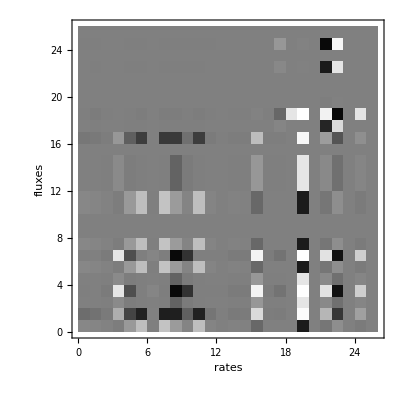

```mathematica
faktor=3;
cjp=ArcTan[cj*faktor]/Pi+0.5;
Print["Normierte Flusskontrollkoeffizienten"];
Show[Graphics[Raster[cjp]],AspectRatio->1,ImagePadding->1,Frame->True,FrameLabel->{"rates","fluxes"}, LabelStyle->Directive[Bold, Medium]]
```

Normierte Konzentrationskontrollkoeffizienten

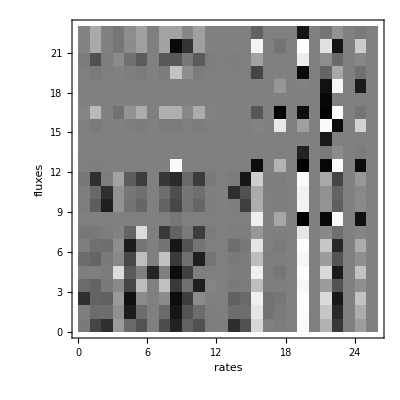

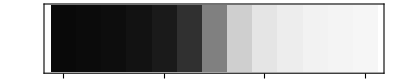

```mathematica
cjs=ArcTan[cs*faktor]/Pi+0.5;
Print["Normierte Konzentrationskontrollkoeffizienten"];
Show[Graphics[Raster[cjs]],AspectRatio->1,ImagePadding->1,Frame->True,FrameLabel->{"rates","fluxes"}, LabelStyle->Directive[Bold, Medium]]

massstab=ArcTan[Table[x/2,{y,1,1},{x,-6,6}]*faktor]/Pi+0.5;
Show[Graphics[Raster[massstab]],AspectRatio->0.2,Frame->True,FrameTicks->{{{0.5,-3},{2.5,-2},{4.5,-1},{6.5,0},{8.5,1},{10.5,2},{12.5,3}},None,None,None}]
```

```mathematica
cjw=MatrixForm[cj]
csw=MatrixForm[cs]
dvdsw=MatrixForm[dvds/.ss]
```

(0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | 3.8865×10^-13
-0.0754342 | -0.0560686 | -0.0233276 | 0.217715 | -0.300557 | -0.762996 | 0.00488336 | -0.853745 | -0.832769 | -0.137236 | -0.767742 | -0.0439441 | -0.000258499 | -0.0244146 | -0.0178584 | 0.684511 | -0.0106264 | -0.0152595 | -5.18898×10^-20 | 6.87781 | 0. | 0.262202 | -0.429878 | 0. | 0.140413 | -2.23955×10^-14
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | 6.01775×10^-14
-0.000380203 | 0.000770658 | -0.0174734 | 0.990816 | -0.225131 | -0.00384565 | 0.0222241 | -0.00430304 | -2.83926 | -0.467896 | -0.00386957 | -0.000221487 | -0.000193627 | -0.0182876 | -0.0174349 | 2.33379 | -0.0132461 | -0.0520262 | -1.76914×10^-19 | 23.4494 | 0. | 0.893956 | -1.46564 | 0. | 0.478728 | 7.59744×10^-14
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -1.61805×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -2.42057×10^-14
-0.000380203 | 0.000770658 | -0.0174734 | 0.990816 | -0.225131 | -0.00384565 | 0.0222241 | -0.00430304 | -2.83926 | -0.467896 | -0.00386957 | -0.000221487 | -0.000193627 | -0.0182876 | -0.0174349 | 2.33379 | -0.0132461 | -0.0520262 | -1.76914×10^-19 | 23.4494 | 0. | 0.893956 | -1.46564 | 0. | 0.478728 | 1.04582×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -3.00862×10^-14
-4.06837×10^-19 | -2.05722×10^-19 | -1.20518×10^-18 | 1.87013×10^-20 | 3.14786×10^-19 | 6.94016×10^-20 | -4.37445×10^-24 | -3.35728×10^-19 | 1.11022×10^-16 | 2.98736×10^-20 | -6.19631×10^-20 | 6.64988×10^-20 | 9.61963×10^-19 | 5.33838×10^-19 | 7.41695×10^-19 | -6.23894×10^-17 | -5.01469×10^-19 | 8.70705×10^-16 | 4.53648×10^-39 | 7.36734×10^-14 | 0. | -1.31887×10^-16 | 6.31062×10^-17 | 0. | -3.02563×10^-16 | -9.35843×10^-14
7.34885×10^-17 | 5.5609×10^-17 | 1.73897×10^-16 | -7.79742×10^-17 | 1.49636×10^-15 | 1.16858×10^-16 | -1.80437×10^-18 | 2.64655×10^-17 | 6.72115×10^-16 | 3.33067×10^-16 | 5.8171×10^-18 | 2.57507×10^-17 | -2.91935×10^-16 | 1.12694×10^-16 | 1.11979×10^-16 | -1.30285×10^-15 | 2.21726×10^-17 | -2.22069×10^-15 | -1.5746×10^-34 | 3.42416×10^-13 | 0. | 8.11327×10^-16 | -2.25303×10^-16 | 0. | 2.22688×10^-16 | -9.00649×10^-13
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | -4.80208×10^-14
0.0319328 | 0.023822 | 0.00844148 | -0.0104143 | 0.108762 | 0.322991 | -0.000233594 | 0.361407 | 0.118357 | 0.0195046 | 0.325001 | 0.0186024 | 0.0000935421 | 0.00883483 | 0.00612717 | -0.0972859 | 0.00340871 | 0.00216875 | 7.3748×10^-21 | -0.977506 | 0. | -0.0372653 | 0.0610962 | 0. | -0.0199561 | 1.01343×10^-12
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -1.28726×10^-11
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -6.644×10^-15
-0.0000163784 | 0.0000331985 | -0.000752722 | 0.0426825 | -0.00969821 | -0.000165663 | 0.00095737 | -0.000185367 | -0.12231 | -0.0201561 | -0.000166693 | -9.54122×10^-6 | -8.3411×10^-6 | -0.000787797 | -0.000751061 | 0.100535 | -0.000570615 | -0.00224119 | -7.62112×10^-21 | 1.01015 | 0. | 0.0385099 | -0.0631368 | 0. | 0.0206227 | -3.88063×10^-14
-1.87541×10^-19 | -1.73236×10^-19 | -9.65642×10^-19 | 4.12273×10^-21 | -2.36897×10^-19 | 1.50209×10^-19 | -1.23629×10^-21 | -5.66027×10^-19 | 7.52746×10^-18 | 3.65632×10^-20 | -1.41092×10^-19 | 8.12238×10^-20 | 8.84908×10^-19 | 7.11821×10^-19 | 6.04603×10^-19 | 2.22045×10^-16 | -5.96303×10^-19 | 5.55034×10^-16 | -1.82252×10^-35 | 1.12573×10^-13 | 0. | 1.27866×10^-16 | 5.11947×10^-16 | 0. | -3.33588×10^-16 | -2.99839×10^-13
-0.0348421 | -0.0258974 | -0.0107747 | 0.10056 | -0.138824 | -0.352418 | 0.00225556 | -0.394334 | -0.384645 | -0.0633876 | -0.35461 | -0.0202972 | -0.000119397 | -0.0112768 | -0.00824857 | 0.316167 | -0.00490821 | -0.00704818 | -2.39672×10^-20 | 3.17677 | 0. | 0.121107 | -0.198555 | 0. | 0.0648549 | 6.34613×10^-12
-0.0000316222 | -0.000442707 | -9.77899×10^-6 | 0.0000912667 | -0.000125994 | -0.00031985 | 2.04712×10^-6 | -0.000357892 | -0.000349099 | -0.0000575298 | -0.00032184 | -0.0000184215 | -1.08363×10^-7 | -0.0000102347 | -7.48629×10^-6 | 0.000286949 | -4.45463×10^-6 | 0.023844 | 1.3415×10^-19 | 0.0028832 | 0. | -0.677865 | 0.671711 | 0. | 0.0000588158 | 1.87998×10^-13
-0.0010291 | -0.0144072 | -0.000318243 | 0.00297014 | -0.0041003 | -0.010409 | 0.0000666204 | -0.0116471 | -0.0113609 | -0.00187222 | -0.0104738 | -0.0005995 | -3.52653×10^-6 | -0.000333072 | -0.00024363 | 0.00933832 | -0.000144969 | -0.103134 | 1. | 46.4848 | 0. | 2.0085 | -2.9054 | 0. | 0.949003 | 3.66973×10^-14
-2.19414×10^-7 | -3.07177×10^-6 | -6.78526×10^-8 | 6.33265×10^-7 | -8.74227×10^-7 | -2.21932×10^-6 | 1.42042×10^-8 | -2.48328×10^-6 | -2.42226×10^-6 | -3.99177×10^-7 | -2.23312×10^-6 | -1.2782×10^-7 | -7.51892×10^-10 | -7.10144×10^-8 | -5.19445×10^-8 | 1.99103×10^-6 | -3.0909×10^-8 | 0.000165444 | 9.30814×10^-22 | 0.0000200054 | 0. | -0.00470345 | 0.00466075 | 0. | 4.08153×10^-7 | -9.43082×10^-15
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-9.37873×10^-11 | -1.31301×10^-9 | -2.90032×10^-11 | 2.70685×10^-10 | -3.73683×10^-10 | -9.48633×10^-10 | 6.07148×10^-12 | -1.06146×10^-9 | -1.03538×10^-9 | -1.70626×10^-10 | -9.54533×10^-10 | -5.46357×10^-11 | -3.21392×10^-13 | -3.03547×10^-11 | -2.22033×10^-11 | 8.51052×10^-10 | -1.32118×10^-11 | 7.0718×10^-8 | 1.979×10^-19 | 8.55125×10^-9 | 0. | -8.9258×10^-7 | 1.46246×10^-7 | 0. | -6.7173×10^-8 | 7.37946×10^-15
-0.000045942 | -0.000643181 | -0.0000142073 | 0.000132596 | -0.00018305 | -0.00046469 | 2.97413×10^-6 | -0.000519959 | -0.000507184 | -0.0000835815 | -0.000467581 | -0.0000267634 | -1.57435×10^-7 | -0.0000148693 | -0.0000108764 | 0.00041689 | -6.47186×10^-6 | 0.0346414 | 1.94898×10^-19 | 0.00418882 | 0. | -0.98483 | 0.975888 | 0. | 0.0000854499 | 7.58903×10^-16
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000133342 | -0.00186676 | -0.0000412351 | 0.000384845 | -0.000531282 | -0.00134871 | 8.63209×10^-6 | -0.00150913 | -0.00147205 | -0.000242586 | -0.0013571 | -0.000077678 | -4.56937×10^-7 | -0.0000431566 | -0.0000315675 | 0.00120998 | -0.0000187839 | 0.100543 | 5.6567×10^-19 | 0.0121576 | 0. | -2.85836 | 2.83241 | 0. | 0.000247977 | 4.30009×10^-13
-9.79351×10^-12 | 0. | 2.63229×10^-11 | -1.84897×10^-12 | 6.97472×10^-11 | 0. | 0. | -5.59629×10^-12 | -7.06995×10^-12 | 0. | -5.59629×10^-12 | -1.39907×10^-12 | -2.25793×10^-11 | -1.1401×10^-11 | -2.36403×10^-11 | 0. | -6.578×10^-12 | 5.84963×10^-9 | 0. | -2.10946×10^-7 | 0. | 0. | -1.16317×10^-8 | 0. | 3.08278×10^-9 | 2.83166×10^-7)

(-0.0208758 | -0.291929 | -0.516079 | 0.113897 | -0.0952976 | -0.211153 | 0.0025547 | -0.236267 | -0.766041 | -0.12624 | -0.212467 | -0.0121612 | -0.0057188 | -0.540127 | -0.217422 | 0.629663 | -0.00365586 | -0.0140368 | -4.77318×10^-20 | 6.32669 | 0. | 0.241191 | -0.395432 | 0. | 0.129162 | -5.55528×10^-14
-0.00762071 | -0.0820391 | -0.0725664 | 0.0691512 | -0.93496 | -0.0770814 | 0.00155106 | -0.0862493 | -1.20646 | -0.198818 | -0.0775609 | -0.00443944 | -0.000804127 | -0.0759479 | -0.0719695 | 0.991673 | -0.0544412 | -0.0221069 | -7.51743×10^-20 | 9.9641 | 0. | 0.379859 | -0.622778 | 0. | 0.203421 | 1.90644×10^-13
-0.496908 | -0.124065 | -0.130523 | 0.11442 | -1.68168 | 0.0461842 | 0.00256646 | 0.0516772 | -2.15924 | -0.355832 | 0.0464714 | 0.00265994 | -0.00144636 | -0.136605 | -0.0945103 | 1.77483 | -0.0524081 | -0.0395655 | -1.34542×10^-19 | 17.8331 | 0. | 0.679847 | -1.11461 | 0. | 0.364069 | 2.53243×10^-13
-0.0850045 | -0.117159 | -0.0226531 | 0.0381039 | -0.291867 | 0.304897 | 0.000854672 | 0.34116 | -0.394494 | -0.0650106 | -0.865146 | 0.0175603 | -0.000251025 | -0.0237087 | -0.0164923 | 0.324262 | -0.0092123 | -0.00722864 | -2.45809×10^-20 | 3.25811 | 0. | 0.124208 | -0.203639 | 0. | 0.0665155 | -1.21918×10^-15
-0.000275191 | 0.000557803 | -0.0126473 | 0.717153 | -0.16295 | -0.00278348 | -0.707715 | -0.00311454 | -2.05506 | -0.338664 | -0.00280079 | -0.000160312 | -0.000140148 | -0.0132366 | -0.0126194 | 1.6892 | -0.0095875 | -0.0376566 | -1.2805×10^-19 | 16.9727 | 0. | 0.647046 | -1.06083 | 0. | 0.346503 | 7.56962×10^-14
-0.0815936 | -0.113792 | -0.0217486 | 0.0368325 | -0.280214 | 0.321562 | 0.000826154 | 0.359808 | -0.380635 | -0.0627268 | -0.83043 | -0.0475323 | -0.000241002 | -0.0227621 | -0.0158351 | 0.312871 | -0.00884607 | -0.0069747 | -2.37173×10^-20 | 3.14365 | 0. | 0.119845 | -0.196485 | 0. | 0.0641788 | 6.5739×10^-14
-0.00471081 | -0.0656576 | -0.0749779 | 0.0611898 | -0.96603 | -0.0476485 | 0.00137249 | -0.0533157 | -1.22105 | -0.201222 | -0.0479449 | -0.00274427 | -0.000830849 | -0.0784717 | -0.0321766 | 1.00366 | -0.00129801 | -0.0223742 | -7.60832×10^-20 | 10.0846 | 0. | 0.384452 | -0.630308 | 0. | 0.20588 | -1.48877×10^-13
-0.0347367 | -0.0259137 | -0.0091827 | 0.0113288 | -0.118312 | 0.736454 | 0.000254105 | -0.393141 | -0.128749 | -0.0212173 | -0.353538 | -0.0202358 | -0.000101756 | -0.00961059 | -0.00666518 | 0.105828 | -0.00370802 | -0.00235918 | -8.02236×10^-21 | 1.06334 | 0. | 0.0405374 | -0.0664609 | 0. | 0.0217084 | 2.63311×10^-14
-0.000226147 | -0.00316603 | -0.0000699347 | 0.000652697 | -0.000901053 | -0.00228742 | 0.00001464 | -0.00255948 | -0.0380546 | -0.000411426 | -0.00230165 | -0.000131742 | -7.74965×10^-7 | -0.0000731935 | -0.0000535384 | 1.69479 | -0.0000318574 | 0.170521 | 5.79853×10^-19 | -76.8576 | 0. | -2.93003 | 4.80377 | 0. | -1.56908 | 4.39943×10^-13
-0.0106559 | -0.148882 | -0.809539 | 0.0793725 | -0.0534418 | -0.107782 | 0.00178033 | -0.120601 | -0.269131 | -0.0443517 | -0.108452 | -0.00620761 | -0.0000459635 | -0.00434114 | -0.338303 | 0.221218 | -0.00214916 | -0.00493146 | -1.67693×10^-20 | 2.22272 | 0. | 0.0847364 | -0.138925 | 0. | 0.0453776 | 3.24497×10^-14
-0.00675176 | -0.0941943 | -0.512673 | 0.0729931 | -0.0389907 | -0.0682922 | 0.00163724 | -0.0764147 | -0.235544 | -0.0388167 | -0.068717 | -0.00393323 | -0.0000335345 | -0.536563 | -0.214477 | 0.193611 | -0.00166434 | -0.00431604 | -1.46766×10^-20 | 1.94534 | 0. | 0.0741617 | -0.121588 | 0. | 0.0397147 | 1.69901×10^-14
-0.036224 | -0.506832 | -0.0120544 | 0.153151 | -0.155311 | -0.366396 | 0.00343519 | -0.409974 | -0.58074 | -0.0957039 | -0.368675 | -0.0211023 | -0.000133578 | -0.0126161 | -1.1494 | 0.477353 | -0.00575074 | -0.0106412 | -3.61853×10^-20 | 4.79623 | 0. | 0.182846 | -0.299775 | 0. | 0.0979168 | -5.4515×10^-14
-0.0003189 | -0.00446455 | -0.0000986179 | 0.000920395 | -0.00127061 | -0.00322558 | 0.0000206445 | -0.00360922 | 4.36958 | -0.000580169 | -0.00324565 | -0.000185775 | -1.09281×10^-6 | -0.000103213 | -0.0000754968 | -2.03335 | -0.0000449235 | 0.240459 | 8.17675×10^-19 | -108.38 | 0. | -4.13175 | 6.77399 | 0. | -2.21262 | -2.91932×10^-13
-2.19674×10^-6 | -0.000030754 | -6.79329×10^-7 | 6.34013×10^-6 | -8.7526×10^-6 | -0.0000222194 | 1.4221×10^-7 | -0.0000248621 | -0.0000242513 | -3.99649×10^-6 | -0.0000223576 | -1.27971×10^-6 | -7.52781×10^-9 | -7.10984×10^-7 | -5.20059×10^-7 | 0.0000199338 | -3.09455×10^-7 | 0.0016564 | 5.63255×10^-21 | -0.746576 | 0. | -0.0284616 | 0.0466626 | 0. | -0.0152416 | -6.24381×10^-16
-1.04727×10^-10 | -1.46616×10^-9 | -3.23861×10^-11 | 3.02258×10^-10 | -4.17269×10^-10 | -1.05928×10^-9 | 6.77966×10^-12 | -1.18527×10^-9 | -1.15615×10^-9 | -1.90528×10^-10 | -1.06587×10^-9 | -6.10084×10^-11 | -3.58879×10^-13 | -3.38952×10^-11 | -2.47932×10^-11 | 9.50319×10^-10 | -1.47529×10^-11 | 7.89666×10^-8 | 2.20984×10^-19 | 9.54868×10^-9 | 0. | -1.11664 | 1.63304×10^-7 | 0. | -7.50081×10^-8 | 8.24021×10^-15
-0.00151367 | -0.0211911 | -0.000468092 | 0.00436868 | -0.00603099 | -0.0153103 | 0.0000979897 | -0.0171313 | -0.0167104 | -0.00275379 | -0.0154055 | -0.000881784 | -5.18705×10^-6 | -0.000489904 | -0.000358348 | 0.0137354 | -0.00021323 | 1.14134 | -1.07326×10^-18 | 0.13801 | 0. | 5.42323 | -2.31368 | 0. | 0.526264 | 4.29303×10^-7
0.0201512 | 0.282114 | 0.00623163 | -0.0581595 | 0.0802896 | 0.203824 | -0.00130452 | 0.228066 | 0.222462 | 0.0366607 | 0.205091 | 0.011739 | 0.0000690543 | 0.00652201 | 0.00477062 | -0.182857 | 0.0028387 | -15.1945 | 2.1029×10^-18 | -1.83731 | 0. | -10.6261 | 10.5761 | 0. | -0.03751 | 2.93324×10^-12
-3.41264×10^-10 | -4.77765×10^-9 | -1.05534×10^-10 | 9.84941×10^-10 | -1.35972×10^-9 | -3.45179×10^-9 | 2.20923×10^-11 | -3.86234×10^-9 | -3.76744×10^-9 | -6.20855×10^-10 | -3.47326×10^-9 | -1.98803×10^-10 | -1.16945×10^-12 | -1.10451×10^-10 | -8.07913×10^-11 | 3.09672×10^-9 | -4.80739×10^-11 | 2.57322×10^-7 | 7.201×10^-19 | 3.11149×10^-8 | 0. | -3.6387 | 5.32145×10^-7 | 0. | -2.44422×10^-7 | 2.68516×10^-14
-0.000126286 | -0.00176799 | -0.0000390533 | 0.000364482 | -0.00050317 | -0.00127735 | 8.17534×10^-6 | -0.00142927 | -0.00139416 | -0.00022975 | -0.00128529 | -0.0000735678 | -4.32759×10^-7 | -0.000040873 | -0.0000298972 | 0.00114596 | -0.00001779 | 0.095223 | 3.06722×10^-19 | 0.0115143 | 0. | -1.54988 | 2.68254 | 0. | -0.946853 | 3.98717×10^-13
-0.00176429 | -0.0246998 | -0.000545596 | 0.00509201 | -0.00702956 | -0.0178453 | 0.000114214 | -0.0199677 | 0.355525 | 0.0585888 | -0.0179563 | -0.00102778 | -6.04588×10^-6 | -0.000571019 | -0.00041768 | -0.292231 | -0.000248535 | 0.00651459 | 2.21527×10^-20 | -2.93627 | 0. | -0.111939 | 0.183523 | 0. | -0.0599451 | -4.77999×10^-15
-0.0159442 | -0.223217 | -0.00493067 | 0.0460176 | -0.0635277 | -0.161272 | 0.00103218 | -0.180453 | -0.176019 | -0.0290071 | -0.162275 | -0.0092883 | -0.000054638 | -0.00516042 | -0.00377466 | 0.144683 | -0.00224607 | -0.00322535 | -1.09678×10^-20 | 1.45374 | 0. | 0.0554206 | -0.0908618 | 0. | 0.0296786 | -4.73365×10^-15
0.013474 | 0.188635 | 0.00416677 | -0.0388882 | 0.0536854 | 0.136286 | -0.000872264 | 0.152496 | -2.71518 | -0.447449 | 0.137134 | 0.00784928 | 0.000046173 | 0.00436093 | 0.00318986 | 2.2318 | 0.00189809 | -0.0497526 | -1.69183×10^-19 | 22.4246 | 0. | 0.854889 | -1.40159 | 0. | 0.457806 | 3.65053×10^-14
0.0138478 | 0.193867 | 0.00428235 | -0.0399669 | 0.0551746 | 0.140067 | -0.00089646 | 0.156726 | 0.152875 | 0.0251931 | 0.140938 | 0.00806701 | 0.0000474538 | 0.0044819 | 0.00327835 | -0.125659 | 0.00195074 | 0.00280126 | 9.52564×10^-21 | -1.26259 | 0. | -0.0481335 | 0.0789147 | 0. | -0.0257762 | 4.11123×10^-15)

(0 | -0.268573 | 0.292695 | 0 | 0 | 0 | -5.47563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250817 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.51862 | 0 | -1.95251 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.00288769 | 0 | 0 | -0.000747668 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.205747 | -0.00348871
-50.7372 | 0 | 0 | 0 | 0 | 0 | 6.57593 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.90763 | 0.0507216
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.204873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.156092 | 0 | 0.183096 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.036322 | 0.0129119 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.27275×10^18 | 0 | 0 | 0 | 2.16174×10^19 | -2.72394×10^20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.105949 | 0 | 0 | 0 | 0.317176 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.6057 | -0.204454
0 | 0 | -0.0287587 | 0.554102 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0443311 | -0.0270209 | 0 | 0
0 | 0 | 0 | -9.68066 | 0 | 3.03255 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58992.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -105.667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121.244 | -21.2159 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.18387 | 1.11879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.69514 | -2.41039×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0666823 | -0.240213 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.52781×10^16 | 0 | 0 | 0 | 8.0443×10^14 | -4.82541×10^17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.40616 | 0 | 0 | 0 | 0 | -53.331 | 0 | 0 | 0 | 0 | -1.72449 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.49918×10^-27 | 0 | 0 | 4.42318×10^-10 | 0 | 0 | 0 | 2.25064×10^-9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -8.75983×10^-28 | 8.47544×10^-28 | 0 | 0 | 0 | 0 | 0 | 1.09668×10^-29 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.90966×10^-7 | 0 | 0 | 0 | 0 | 3.04187×10^-9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.13103×10^-7 | 0 | 0 | 2.53551×10^-11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.6732×10^-30 | 7.2475×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.49298×10^-7 | 0 | 1.08072×10^-11 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.87454×10^-7 | 0 | 0 | 0 | 2.45179×10^-10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.07201×10^-25 | 0 | 0.251305 | 0.2312 | 0.2312 | 0.2312 | 0 | 0 | 0 | 0)